```mathematica
L[th_,u_,v_,imps_]:= imps 1/(√(2 Pi u))Exp[-th^2/(2 u^2)]+1/(√(2 Pi u))Exp[-th^2/(2 v^2)];
```

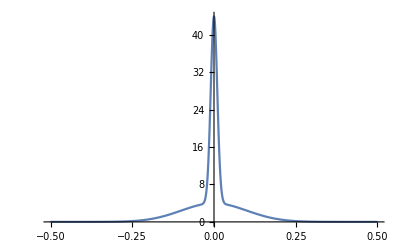

```mathematica
Plot[L[th,0.01,0.1,10], {th,-0.5,0.5},PlotRange->All]
```

```mathematica
L[th,0.01,0.1,10]PDF[UniformDistribution[{-0.5,0.5}],th]//FullSimplify
```

Piecewise[{{39.8942 ⅇ^(-5000. th^2)+3.98942 ⅇ^(-50. th^2), -0.5≤th≤0.5}, {0, True}}]

```mathematica
(*1D Z:*)
Z=∫_-0.5^0.5 L[th,0.01,0.1,10]PDF[UniformDistribution[{-0.5,0.5}],th]ⅆth
```

2.

```mathematica
Log[Z]
```

0.693147

```mathematica
L[th,u0,v0,D0]
```

(D0 ⅇ^(-th^2/(2 u0^2)))/(√(2 π) √u0)+(ⅇ^(-th^2/(2 v0^2)))/(√(2 π) √u0)

```mathematica
a=Log[D0/(√(2 π) √u0)]-th^2/(2 u0^2);
b=-Log[√(2 π) √u0]-th^2/(2 v0^2);
```

```mathematica
b//CForm
```

-Power(th,2)/(2.*Power(v0,2)) - Log(Sqrt(2*Pi)*Sqrt(u0))